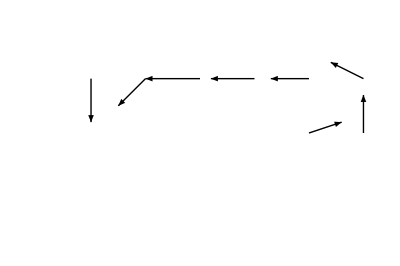

```mathematica
baseVectorField=({{{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}}, {{0,0}, {0,-0.8}, {-0.5,-0.5}, {-1,0}, {-0.8,0}, {-0.7,0}, {0-0.6,0.3}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0.6,0.2}, {0,0.7}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}}, {{0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}, {0,0}}});
tableRows[table_]:=Length[table];
tableColumns[table_]:=Length[table[[1]]];
mapTable[f_,table_]:=Map[
f[
#1,
table[[
#1[[1]],
#1[[2]]
]]
]&,
Table[
{i,j},
{i,1,tableRows[table]},
{j,1,tableColumns[table]}
],
{2}];
tableTranspose[table_]:=Transpose[
mapTable[
table[[
tableRows[table]-#1[[1]]+1,
#1[[2]]
]]&,
table
]];
Graphics[
{
mapTable[Arrow[{{0.5,0.5}+#1,{0.5,0.5}+#1+#2}]&,tableTranspose[baseVectorField]]
}]
```